-0.0334073

General::ovfl: Overflow occurred in computation.

General::munfl: Exp[-1.50713×10^19] is too small to represent as a normalized machine number; precision may be lost.

General::ovfl: Overflow occurred in computation.

General::munfl: Exp[-1.27317×10^18] is too small to represent as a normalized machine number; precision may be lost.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::munfl: Exp[-2.43866×10^20] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-0.00247634

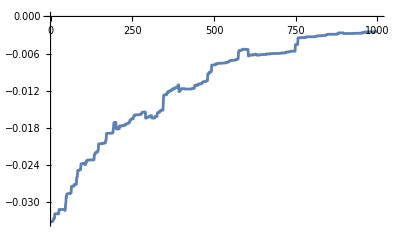

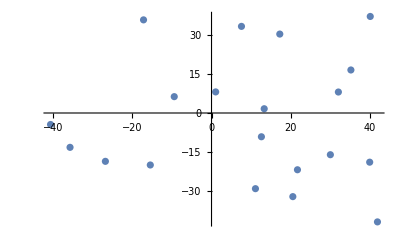

```mathematica
numb=20;
bfield={1,0};
(*Ub,J*)
latvec={100,100};
(*10-6m/2d*)
sigma=1;
(*10-6m*)
epsilon=10;
(*J*)
epsilonB=-1;
(*J*)
b=8.314462618*298/(6.022140857*10^23);
(*J*)
cutoff=10;
(*10-6m*)
config=Table[RandomReal[],numb,2]*latvec1[[1]]-latvec1[[1]]/2;
(*random inital config*)
diff=b/(4*Pi*8.9*10^-4*10^-6);
(*at normal temperature, assume r=10^-6m, unit=m^2/s*)

deltat=0.01;
(*s*)
msdroot=10^6(4*deltat*diff)^0.5;
(*10-6m*)


configEpbc[con_]:=Module[{dist,utot},dist=Flatten[Table[If[i==j &&a==b==0,Nothing,{VectorAngle[bfield,con[[i]]-con[[j]]+{a,b}*latvec],EuclideanDistance[con[[i]],con[[j]]+{a,b}*latvec]}],{i,Length[con]},{j,Length[con]},{a,-1,1},{b,-1,1}],3];
utot=Sum[If[i[[2]]>cutoff,0,4*epsilon*((sigma/i[[2]])^12-(sigma/i[[2]])^6)+epsilonB*(sigma/i[[2]])^3*(1-3*Cos[i[[1]]])],{i,dist}];
N[utot/2]];
(*potential energy of config in PBC,J*)



force[i_,con_]:=Module[{dist,totf},

dist=Flatten[Table[If[i==j &&a==b==0,Nothing,{VectorAngle[bfield,con[[i]]-con[[j]]+{a,b}*latvec],EuclideanDistance[con[[i]],con[[j]]+{a,b}*latvec],con[[i]]-con[[j]]+{a,b}*latvec}],{j,Length[con]},{a,-1,1},{b,-1,1}],2];

totf=Total[Table[If[y[[2]]>cutoff,{0,0},(D[4*epsilon*((sigma/rr)^12-(sigma/rr)^6)+epsilonB*(sigma/rr)^3*(1-3*Cos[y[[1]]]),rr]/.rr->y[[2]])*y[[3]]/Norm[y[[3]]]],{y,dist}]]];
(*total force(vector) of atom(i), N*)




randmove[]:=Module[{localConfig=config,cho,dvec,oldE,newE,oldf,newf},
oldE=configEpbc[config];
cho=RandomInteger[{1,Length[config]}];

oldf=force[cho,config];
dvec=(diff*deltat*oldf/b)*10^-6+Table[RandomVariate[NormalDistribution[0,1]]*msdroot,2];
localConfig[[cho]]=localConfig[[cho]]+dvec;
newE=configEpbc[localConfig];
newf=force[cho,localConfig];
If[RandomReal[]<N[Exp[-(1/b)*(newE-oldE+Dot[0.5*(oldf+newf),dvec]+diff*deltat*((Norm[newf-oldf])^2+Dot[2*(newf-oldf),oldf])/(4*b))]],localConfig,config]];
conE={};
configEpbc[config]
Table[config=randmove[];conE=Append[conE,configEpbc[config]],1000];
configEpbc[config]
ListLinePlot[conE]
ListPlot[config]
```